## Task1

```mathematica
(*Аппроксимирующий многочлен 1 степени*)
```

```mathematica
X = {0.1,0.2,0.3,0.4};
F = {-1.083,2.067,-5.091,8.001};
n = Length[X]-1;
Do[{Subscript[x, i]= X[[i+1]],Subscript[f, i]= F[[i+1]]},{i,0,n}]
```

```mathematica
ϵ = 1/2*10^-3; M1 = 1;M2 = 2;
```

```mathematica
(*Вычисляем необходимые постоянные величины*)
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2M1}];
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[f, k] Subscript[x, k]^i,{ i,0,M1}];
```

```mathematica
(*Формируем систему линейных уравнений*)
eqv=Table[∑_(i=0)^M1 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,M1}]
```

{4. a_0+1. a_1==3.894,1. a_0+0.3 a_1==1.9782}

```mathematica
(*Решаем полученную систему*)
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
(*Записываем аппроксимирующий многочлен*)
P[x_]=(∑_(i=0)^M1 Subscript[a, i]*x^i)/.Koef
```

-4.05+20.094 x

```mathematica
(*Строим аппроксимирующий многочлен с помощью встроенной функции Fit*)
Tbl=Table[{Subscript[x, k],Subscript[f, k]},{k,0,n}];
Fun=Table[x^i,{i,0,M1}];
P1[x_]=Fit[Tbl,Fun,x]
```

-4.05+20.094 x

```mathematica
P[x] == P1[x]
```

True

```mathematica
(*Вычисляем среднее квадратическое отклонение*)
L=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[f, k])^2)//N
```

4.22494

```mathematica
L<ϵ
```

False

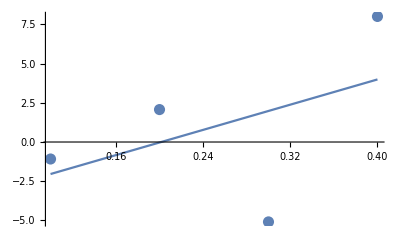

```mathematica
(*Изображаем исходную систему точек
и полученный аппроксимирующий многочлен в одной системе координат*)
Gr1 = ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2 = Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

```mathematica
(*Аппроксимирующий многочлен 2 степени*)
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2M2}];Do[ Subscript[c, i]=∑_(k=0)^n Subscript[f, k] Subscript[x, k]^i,{ i,0,M2}];
```

```mathematica
eqv=Table[∑_(i=0)^M2 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,M2}]
```

{4. a_0+1. a_1+0.3 a_2==3.894,1. a_0+0.3 a_1+0.1 a_2==1.9782,0.3 a_0+0.1 a_1+0.0354 a_2==0.89382}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^M2 Subscript[a, i]*x^i)/.Koef
```

8.3775-104.181 x+248.55 x^2

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[f, k]},{k,0,n}];Fun=Table[x^i,{i,0,M2}];P1[x_]=Fit[Tbl,Fun,x]
```

8.3775-104.181 x+248.55 x^2

```mathematica
L=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[f, k])^2)//N
```

3.41649

```mathematica
L<ϵ
```

False

```mathematica
k1=L/ϵ
```

6832.98

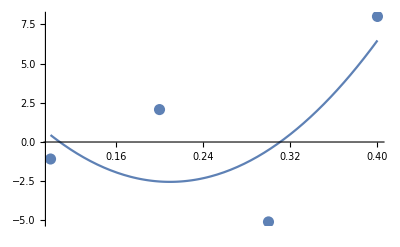

```mathematica
Gr1 = ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2 = Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

```mathematica
Task 2
```

2 Task

```mathematica
(*увеличим степень аппроксимации*)
M3 =3;
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2M3}];Do[ Subscript[c, i]=∑_(k=0)^n Subscript[f, k] Subscript[x, k]^i,{ i,0,M3}];
```

```mathematica
eqv=Table[∑_(i=0)^M3 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,M3}]
```

{4. a_0+1. a_1+0.3 a_2+0.1 a_3==3.894,1. a_0+0.3 a_1+0.1 a_2+0.0354 a_3==1.9782,0.3 a_0+0.1 a_1+0.0354 a_2+0.013 a_3==0.89382,0.1 a_0+0.0354 a_1+0.013 a_2+0.00489 a_3==0.39006}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^M3 Subscript[a, i]*x^i)/.Koef
```

-45.099+746.35 x-3571.2 x^2+5093. x^3

```mathematica
L=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[f, k])^2)//N
```

7.42252×10^-12

```mathematica
L<ϵ
```

True

```mathematica
ϵ -L
```

0.0005

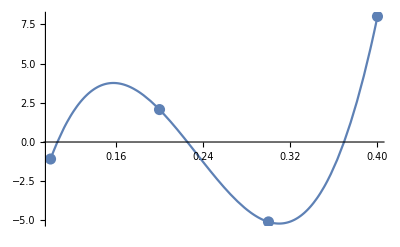

```mathematica
Gr1 = ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2 = Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```